# Timestamp Demodulation

## Last Updated: 04/26/2023

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-04-26";
```

```mathematica
(*run ID*)
ridDJ=19222;
```

## Setup

## Imports

```mathematica
(*turn off messages*)
ParallelEvaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];
];
```

```mathematica
(*import packages*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["Utilities`CleanSlate`"]
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Sided Conversion

```mathematica
(*convert double-sided to single-sided*)
GetSingleSidedX[data_List]:=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]];
```

```mathematica
GetSingleSidedY[data_List]:=With[
{trimmedData=If[OddQ[#2],#1[[;;(#2-1)/2]],#1[[;;(#2-2)/2]]]&[data,Length[data]]},
Return[(2*#1-UnitVector[#2,1]*#1[[1]])&[trimmedData,Length[trimmedData]]]
];
```

### Dataset Processing

```mathematica
(*import and demodulate dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut;

(*return dataset*)
Return[results];
];
```

```mathematica
(*import*)
numCounts=Import[filenameDJ,{"/datasets/num_counts"}];
th0=Import[filenameDJ,{"/datasets/results"}][[1]];
```

```mathematica
freqArrMHz=Range[3,3.5,0.001];
freqArrMHz//Length
```

501

```mathematica
(*process*)
AbsoluteTiming[
th1=ⅈ*(2*π*1*^6)*th0;
th2=ParallelMap[
Total[Exp[#*th1]]&,
freqArrMHz
];
th2/=numCounts;
]
{th30,th31}=Transpose[AbsArg[th2]];
```

{154.55,Null}

```mathematica
(*mhz1mhz2500hz=th2;*)
(*mhz1700mhz171010hz=th2;*)
(*mhz1703mhz17051hz=th2;*)
(*mhz1540mhz155010hz=th2;*)
```

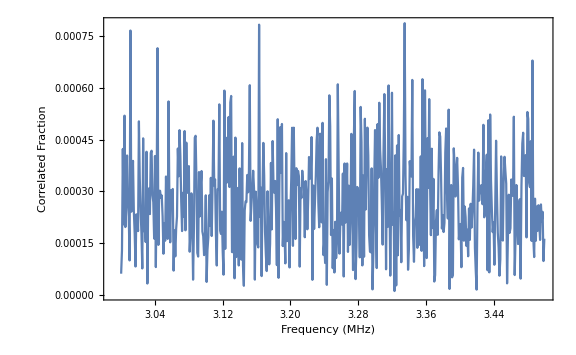

```mathematica
(*plot*)
amplitudePlot=ListLinePlot[
Transpose[{freqArrMHz,th30}],
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RID: "<>ToString[ridDJ],{Black,Directive[15]}]}
}
]
```

```mathematica
Ordering[Abs[th2],5]
```

{130,584,539,383,764}

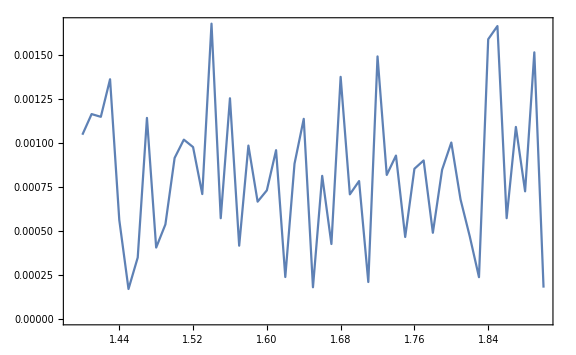
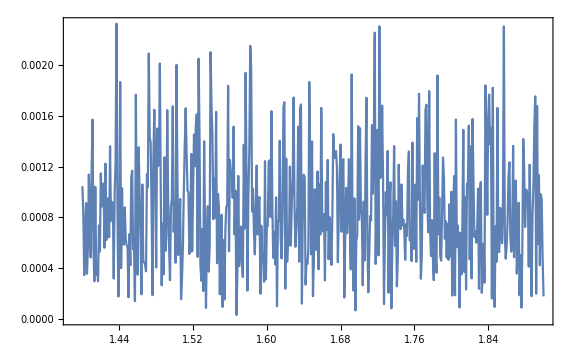
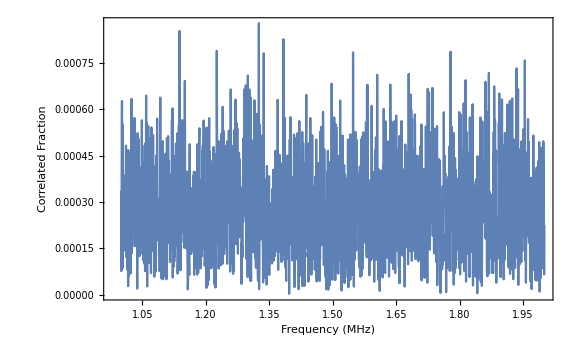
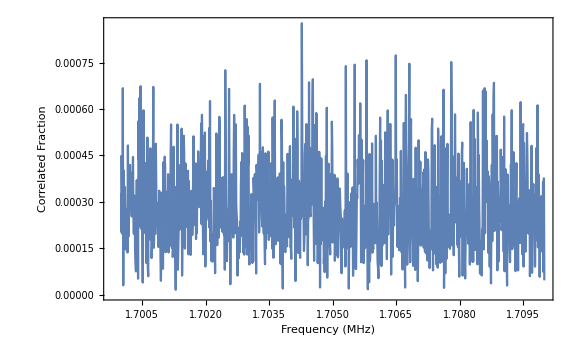
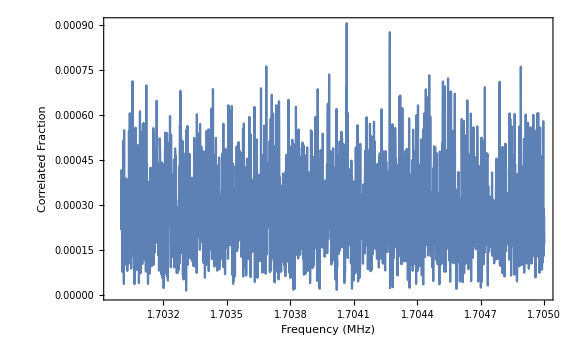
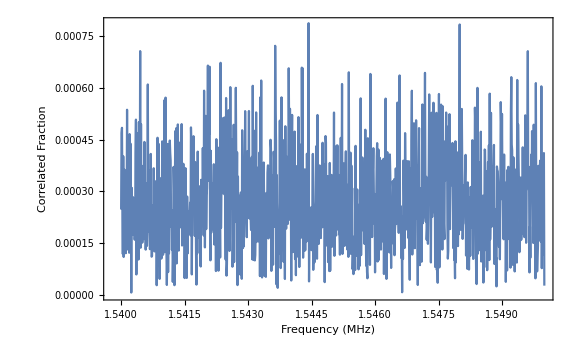
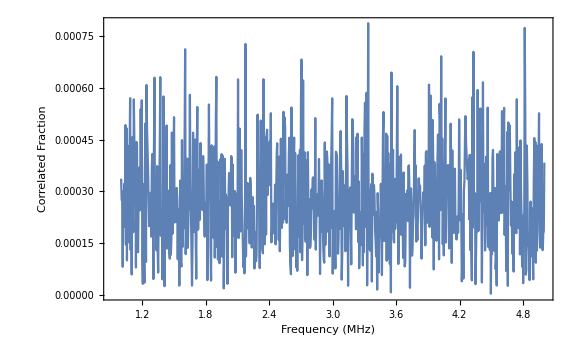
```mathematica
(*store res*)
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics-
```

## Import

## Find Files

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenameDJ=SelectFirst[filenamesAll,StringContainsQ[#,ToString[ridDJ]]&];
```

## Extract Values

```mathematica
(*import and process data*)
AbsoluteTiming[
datasets=ParallelMap[
ProcessDataset,
filenamesAll
];
]
```

{4.57324,Null}

## Plot

## Process Data

```mathematica
(*format data for plots*)
densityPlotData=Join@@datasets[[;;,;;,;;]];
```

```mathematica
(*(*format data for 4d plot (2d plot, 2d color)*)
th0=Join@@datasets;
{th10,th11}={#[[;;2]],#[[3;;]]}&[Transpose[th0]];
th1=Join[th10,{Transpose[th11]}]//Transpose;*)
```

## Plot!

```mathematica
(*intensity plot*)
amplitudeDensityPlot=ListDensityPlot[
densityPlotData[[;;,;;3]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim"<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Stray Field Compensation",{Black,Directive[15]}]}
}
];
```

```mathematica
(*phase plot*)
phaseDensityPlot=ListDensityPlot[
densityPlotData[[;;,{1,2,4}]],
PlotLegends->Automatic,
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim"<>" Voltage (V)",{Black,Directive[15]}],None},
{Style["Secular Frequency (MHz)",{Black,Directive[15]}],Style["Stray Field Compensation",{Black,Directive[15]}]}
}
];
```

## Summary

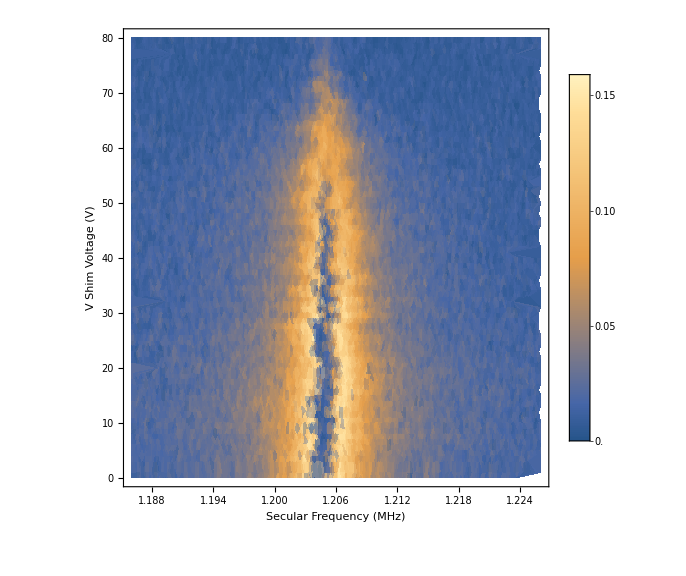
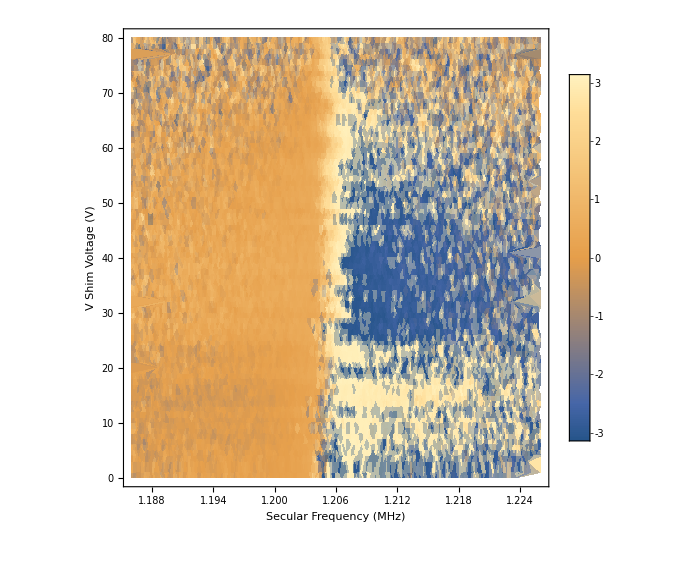

```mathematica
(*Print["Shim Voltage (V): "<>ToString[shimVoltage[[1]]]]
Print["Modulation Amplitude (V): "<>ToString[modulationAmplitudes[[1]]]]*)
{amplitudeDensityPlot,phaseDensityPlot}
```

## Deprecated

## Plotting

```mathematica
(*ListPointPlot3D[{th0[[;;,;;3]]},PlotStyle->Hue/@th0[[;;,4]]]*)
```

```mathematica
(*(*3d plot*)
amplitude3DPlot=ListPlot3D[
densityPlotData,
ImageSize->Large,
PlotRange->Full,
AxesLabel->{"Secular Frequency (MHz)","Voltage (V)","Signal Amplitude"}
];*)
```

```mathematica
(*(*signal plots*)
{amplitudePlot,phasePlot}={
ListLinePlot[
correlatedAmplitude,
DataRange->xRange,
PlotRange->Full,
FrameLabel->{ 
{Style["Correlated Fraction",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Amplitude - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
],
ListLinePlot[
correlatedPhase/π,
DataRange->xRange,
PlotRange->Full,
FrameLabel->{ 
{Style["Phase (π rad.)",{Black,Directive[15]}],None},
{Style["Frequency (MHz)",{Black,Directive[15]}],Style["Correlated Signal Phase - RIDs: "<>ToString[ridList],{Black,Directive[15]}]}
}
]
};*)
```